```mathematica
Needs["MaTeX`"];
(*PREDEFINED LABEL STYLE*)
labstyle={FontFamily->"Latin Modern Roman",FontSize->20};
magn=2;
IS=400;
thick=0.008;
thin=0.006;
dash={0.015,0.02};
pointsize=0.03;

(*decomposition code*)
(*Define Pauli matrices*)σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
id=IdentityMatrix[2];
(*Labels and matrices*)
pauliLabels={"I","σx","σy","σz"};
pauliMatrices={id,σx,σy,σz};

(*decomposition of 2 spins*)
n=2;
(*Generate all combinations*)
tuples=Tuples[Range[4],n];(*1-based indexing*)basisOps=KroneckerProduct@@@(pauliMatrices[[#]]&/@tuples);
basisLabels=StringRiffle[pauliLabels[[#]]&/@#," ⊗ "]&/@tuples;

(*Count number of non-identity terms*)
nonIdentityCounts=Count[#,x_/;x!=1]&/@tuples;
decompose1d[M_] := Tr[M. #]/2 & /@ {σx, σz}; (*a shorter single qubit decomp*)

(*Decomposition function*)
DecomposeSpinOperators[M_]:=Module[{coeffs,assoc,filtered},coeffs=Table[Tr[ConjugateTranspose[b].M]/8//FullSimplify,{b,basisOps}];
assoc=AssociationThread[Transpose[{basisLabels,nonIdentityCounts}]->coeffs];
filtered=Select[assoc,Chop[#]=!=0&];
<|"SingleQubitTerms"->KeySelect[filtered,#[[2]]==1&],"TwoQubitTerms"->KeySelect[filtered,#[[2]]==2&],"ThreeQubitTerms"->KeySelect[filtered,#[[2]]==3&]|>]
```

```mathematica
(*qubit parameters*)pars1={θ1->0.0,θ2->0.0,g1->53,g2->74,g3->47};

pars2={θ1->0.0,θ2->0.0,g1->60,g2->72,g3->43};
(*idle exchange for the aligned-axis case*)

Rot1=RotationMatrix[θ1,n1//Normalize];
Rot2=RotationMatrix[θ2,n2//Normalize];Jidle[gL_,gM_,gS_]:=((gM-gL)^2-(2 gS-gL-gM)^2)/(2 (2 gS-gL-gM))//N;
(*single-qubit Hamiltonian for qubit 1*)
Clear[H1,H2,Hint,Hfull];
H1[J12_,J23_]:=((1/2) (g1 KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4) Sum[J12 Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+J23 Rot2[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])/. pars1;

(*single-qubit Hamiltonian for qubit 2*)
H2[J12_,J23_]:=((1/2) (g1 KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4) Sum[J12 Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+J23 Rot2[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])/. pars2;
Clear[Hint,Hfull];
parsint={
θint->0.00
}
n1={0,1,0};
n2={0,1,0};
nint={0,1,0};
Rotint=RotationMatrix[θint,nint//Normalize]/.parsint;
Hint[Jint_]:=(Jint/4 Sum[Rotint[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j]],{i,1,3},{j,1,3}])/. parsint;
Hfull[J12a_,J23a_,J12b_,J23b_,Jint_]:=KroneckerProduct[H1[J12a,J23a],IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],H2[J12b,J23b]]+Hint[Jint];


n1={0,1,0};
n2={0,1,0};

Rot1=RotationMatrix[θ1,Normalize[n1]];
Rot2=RotationMatrix[θ2,Normalize[n2]];

j12Guess1=Jidle[g1,g2,g3]/. pars1;
j12Guess2=Jidle[g1,g2,g3]/. pars2;

j23arr=Range[0,0.3,0.01];
j12arr1=Range[Max[0,j12Guess1-3.0],j12Guess1+3.0,0.01];
j12arr2=Range[Max[0,j12Guess2-3.0],j12Guess2+3.0,0.01];

X1=ParallelTable[With[{es=Eigensystem[N[H1[j12,j23]]]},Transpose[SortBy[Transpose[es],First]]],{j12,j12arr1},{j23,j23arr}];

eigval1=X1[[All,All,1]];
eigvect1=X1[[All,All,2]];
eigval1=eigval1-eigval1[[All,All,1]];

X2=ParallelTable[With[{es=Eigensystem[N[H2[j12,j23]]]},Transpose[SortBy[Transpose[es],First]]],{j12,j12arr2},{j23,j23arr}];

eigval2=X2[[All,All,1]];
eigvect2=X2[[All,All,2]];
eigval2=eigval2-eigval2[[All,All,1]];
```

{θint→0.}

```mathematica
ths=10^-3;

de1=eigval1[[All,All,3]]-eigval1[[All,All,2]];
pos1=Position[Chop[de1,ths],0];
curve1=Table[{j12arr1[[p[[1]]]],j23arr[[p[[2]]]]},{p,pos1}];

de2=eigval2[[All,All,3]]-eigval2[[All,All,2]];
pos2=Position[Chop[de2,ths],0];
curve2=Table[{j12arr2[[p[[1]]]],j23arr[[p[[2]]]]},{p,pos2}];

best1=
First@MinimalBy[Flatten[Table[{j12arr1[[i]],j23arr[[j]],de1[[i,j]]},{i,Length[j12arr1]},{j,Length[j23arr]}],1],Last];

best2=First@MinimalBy[Flatten[Table[{j12arr2[[i]],j23arr[[j]],de2[[i,j]]},{i,Length[j12arr2]},{j,Length[j23arr]}],1],Last];

j12Idle1=best1[[1]];
j23Idle1=best1[[2]];
gapIdle1=best1[[3]];

j12Idle2=best2[[1]];
j23Idle2=best2[[2]];
gapIdle2=best2[[3]];

{j12Guess1,j12Idle1,j23Idle1,gapIdle1}
{j12Guess2,j12Idle2,j23Idle2,gapIdle2}
```

{9.81818,9.81818,0.,7.10543×10^-15}

{21.4348,21.4348,0.,7.10543×10^-15}

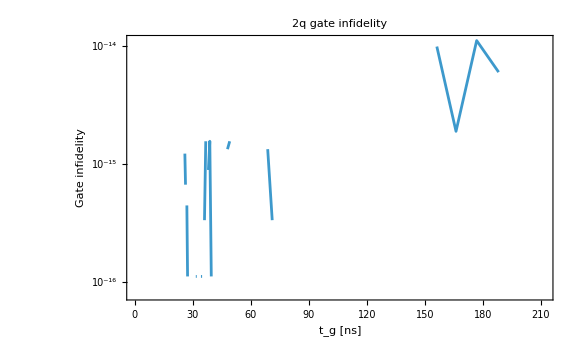

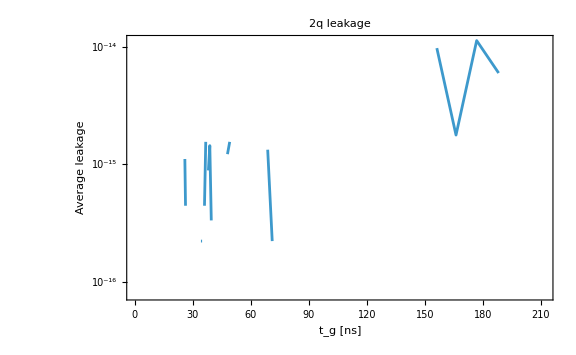

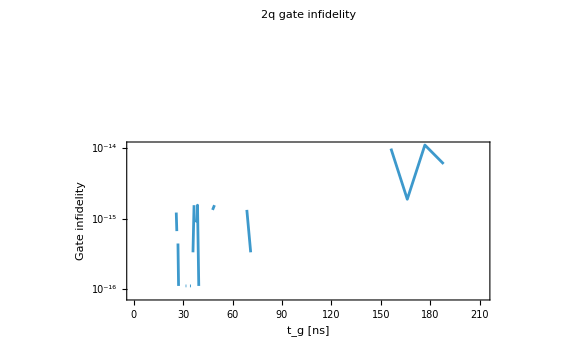

```mathematica
{i1,j1}=First@Position[de1,gapIdle1];
{i2,j2}=First@Position[de2,gapIdle2];

eigtot=KroneckerProduct[eigvect1[[i1,j1,2;;3]],eigvect2[[i2,j2,2;;3]]];

eigtotMatrix=N[Transpose[eigtot]];
Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];

H1idle=N[H1[j12Idle1,j23Idle1]]//Chop;
H2idle=N[H2[j12Idle2,j23Idle2]]//Chop;

HidleFull=N[KroneckerProduct[H1idle,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],H2idle]]//Chop;

HfullGate[Jint_]:=N[HidleFull+Hint[Jint]]//Chop;

Delta=(g3/. pars1)-(g3/. pars2);

tGate[Jint_]:=1/Sqrt[Delta^2+Jint^2];
tGateNs[Jint_]:=1000 tGate[Jint];

Utarget[Jint_]:=Module[{tg,a,c},tg=tGate[Jint];
a=2 Pi Jint tg/4;
c=2 Pi Delta tg/2;
DiagonalMatrix[{Exp[-I a],-Exp[I a+I c],-Exp[I a-I c],Exp[-I a]}]];


Uproj[Jint_]:=Module[{tg,U},tg=tGate[Jint];
U=MatrixExp[-I 2 Pi HfullGate[Jint] tg];
ConjugateTranspose[eigtotMatrix].U.eigtotMatrix];

gateFidelity[Jint_]:=Module[{K,Uid,d=4},K=Uproj[Jint];
Uid=Utarget[Jint];
Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))]];

gateInfidelity[Jint_]:=1-gateFidelity[Jint];

avgLeakage[Jint_]:=Module[{K,d=4},K=Uproj[Jint];
Re[1-Tr[ConjugateTranspose[K].K]/d]];

jintMin=2;
jintMax=40.0;
djint=0.5;

infidelityData=Table[{tGateNs[Jint],gateInfidelity[Jint]},{Jint,jintMin,jintMax,djint}];

leakageData=Table[{tGateNs[Jint],avgLeakage[Jint]},{Jint,jintMin,jintMax,djint}];

ListLogPlot[infidelityData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",ImageSize->Large]

ListLogPlot[leakageData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",ImageSize->Large]
phiCPhase[Jint_]:=2 Pi Jint tGate[Jint];
phiCPhaseModPi[Jint_]:=Mod[phiCPhase[Jint],Pi];

longGatePoint2={202,10^-3};
shortGatePoint2={246,10^-3};

ListLogPlot[infidelityData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",ImageSize->Large,Epilog->{Red,PointSize[0.02],Point[longGatePoint2],Point[shortGatePoint2],Black,Inset[Style[Row[{"ϕ = ",NumberForm[phiCPhaseModPi[jintMin]/Pi,{4,2}],"π"}],14,Background->White],{208,10^-3}],Inset[Style[Row[{"ϕ = ",NumberForm[phiCPhaseModPi[jintMax]/Pi,{4,2}],"π"}],14,Background->White],{238,10^-3}]}]
```

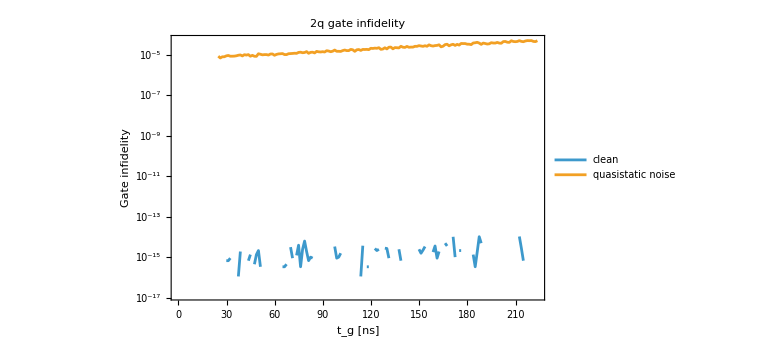

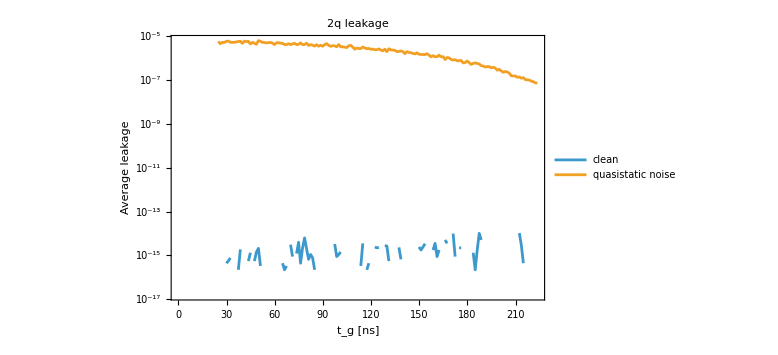

```mathematica
ClearAll[HdJ12Q1,HdJ12Q2,HdJ12Full1,HdJ12Full2,HintFull,UprojQS,oneSampleQS,averagedMetricsQS];

HdJ12Q1=N[(1/4) Sum[Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]/. pars1]//Chop;

HdJ12Q2=N[(1/4) Sum[Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]/. pars2]//Chop;

HdJ12Full1=KroneckerProduct[HdJ12Q1,IdentityMatrix[8]];
HdJ12Full2=KroneckerProduct[IdentityMatrix[8],HdJ12Q2];
HintFull=N[Hint[1.0]]//Chop;

sigmaJ12QS=5.3*10^-4;
sigmaJintQS=1.06*10^-3;

UprojQS[Jint_?NumericQ]:=Module[{tg,d1,d2,dint,Hnoisy,U},tg=tGate[Jint];
d1=RandomVariate[NormalDistribution[0,sigmaJ12QS]];
d2=RandomVariate[NormalDistribution[0,sigmaJ12QS]];
dint=RandomVariate[NormalDistribution[0,sigmaJintQS]];
Hnoisy=HidleFull+j12Idle1 d1 HdJ12Full1+j12Idle2 d2 HdJ12Full2+Jint (1+dint) HintFull;
U=MatrixExp[-I 2 Pi Hnoisy tg];
ConjugateTranspose[eigtotMatrix].U.eigtotMatrix];

oneSampleQS[Jint_?NumericQ]:=Module[{K,Uid,d=4,fidelity,leakage},K=UprojQS[Jint];
Uid=Utarget[Jint];
fidelity=Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))];
leakage=Re[1-Tr[ConjugateTranspose[K].K]/d];
<|"Infidelity"->1-fidelity,"Leakage"->leakage|>];

averagedMetricsQS[Jint_?NumericQ,nSamples_:200]:=Module[{samples},samples=Table[oneSampleQS[Jint],{nSamples}];
<|"Infidelity"->Mean[samples[[All,"Infidelity"]]],"Leakage"->Mean[samples[[All,"Leakage"]]]|>];

nSampQS=200;
ClearAll[jFromTGateNs];

jFromTGateNs[tgNs_?NumericQ]:=Module[{tg=tgNs/1000.},Sqrt[1/tg^2-Delta^2]];

ntGrid=160;

tgNsMin=tGateNs[jintMax];
tgNsMax=tGateNs[jintMin];

tgNsGrid=Subdivide[tgNsMin,tgNsMax,ntGrid-1];

jintList=jFromTGateNs/@tgNsGrid;

infidelityCleanData=Table[{tGateNs[Jint],gateInfidelity[Jint]},{Jint,jintList}];

leakageCleanData=Table[{tGateNs[Jint],avgLeakage[Jint]},{Jint,jintList}];

qsMetricsData=Table[With[{m=averagedMetricsQS[Jint,nSampQS]},{tGateNs[Jint],m["Infidelity"],m["Leakage"]}],{Jint,jintList}];

infidelityQSData=qsMetricsData[[All,{1,2}]];
leakageQSData=qsMetricsData[[All,{1,3}]];

ListLogPlot[{infidelityCleanData,infidelityQSData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",PlotLegends->{"clean","quasistatic noise"},ImageSize->Large]

ListLogPlot[{leakageCleanData,leakageQSData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",PlotLegends->{"clean","quasistatic noise"},ImageSize->Large]
```

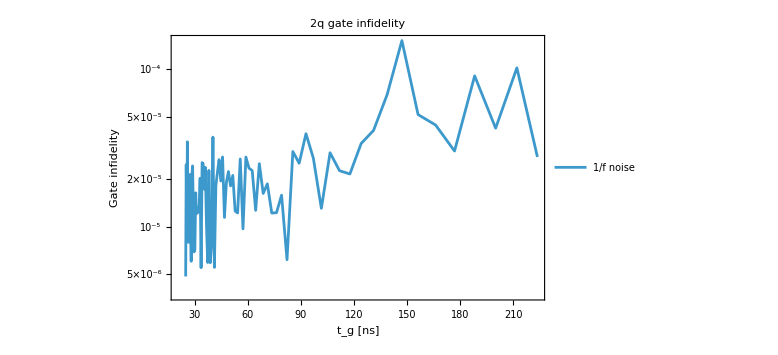

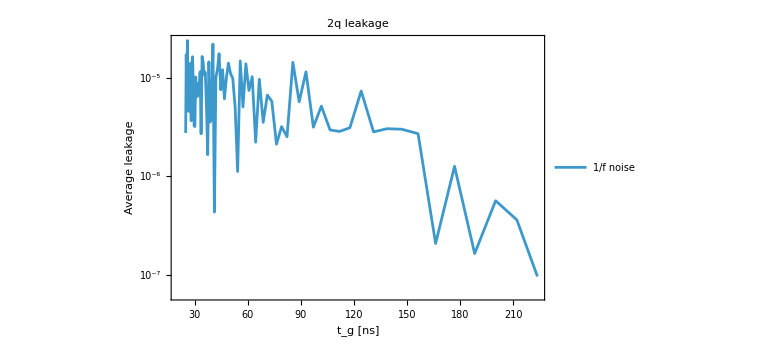

```mathematica
ClearAll[noiseSpec1f,noiseTrace1f,gateDts,gateData,oneSample1f,averagedMetrics1f,scan1f];

noiseSpec1f[fLowHz_:1.,fHighHz_:10.*^6,window_:20]:=noiseSpec1f[fLowHz,fHighHz,window]=Module[{edgesHz},edgesHz=Exp@Subdivide[Log[fLowHz],Log[fHighHz],window];
<|"fMHz"->Sqrt[Most[edgesHz] Rest[edgesHz]]/10.^6,"aUnit"->Sqrt[Log[Rest[edgesHz]/Most[edgesHz]]]|>];

noiseTrace1f[nPts_Integer?Positive,dtStepUs_,amp1Hz_,spec_Association]:=Module[{phi,a},phi=RandomReal[{0,2 Pi},Length[spec["fMHz"]]];
a=amp1Hz spec["aUnit"];
Table[Total[a Cos[2 Pi spec["fMHz"] (k dtStepUs)+phi]],{k,0,nPts-1}]];

gateDts[tg_,dtStepUs_]:=With[{n=Max[1,Ceiling[tg/dtStepUs]]},Join[ConstantArray[dtStepUs,n-1],{tg-(n-1) dtStepUs}]];

gateData[Jint_?NumericQ,dtStepUs_]:=gateData[Jint,dtStepUs]=Module[{tg,dts,Uid},tg=tGate[Jint];
dts=gateDts[tg,dtStepUs];
Uid=Utarget[Jint];
<|"tgNs"->1000. tg,"dts"->dts,"nSeg"->Length[dts],"Uid"->Uid|>];

oneSample1f[Jint_?NumericQ,spec_Association,dtStepUs_,ampJ12_:2.5*10^-4,ampJint_:5*10^-4]:=Module[{gd,dts,nSeg,n12a,n12b,nint,U,K,Uid,d=4,fid,leak},gd=gateData[Jint,dtStepUs];
dts=gd["dts"];
nSeg=gd["nSeg"];
Uid=gd["Uid"];
n12a=noiseTrace1f[nSeg,dtStepUs,ampJ12,spec];
n12b=noiseTrace1f[nSeg,dtStepUs,ampJ12,spec];
nint=noiseTrace1f[nSeg,dtStepUs,ampJint,spec];
U=Fold[Dot,IdentityMatrix[Length[HidleFull]],Reverse@MapThread[MatrixExp[-I 2 Pi #1 (HidleFull+j12Idle1 #2 HdJ12Full1+j12Idle2 #3 HdJ12Full2+Jint (1+#4) HintFull)]&,{dts,n12a,n12b,nint}]];
K=ConjugateTranspose[eigtotMatrix].U.eigtotMatrix;
fid=Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))];
leak=Re[1-Tr[ConjugateTranspose[K].K]/d];
<|"Infidelity"->1-fid,"Leakage"->leak|>];

averagedMetrics1f[Jint_?NumericQ,spec_Association,dtStepUs_,ampJ12_:2.5*10^-4,ampJint_:5*10^-4,nSamples_:20]:=Module[{samples},samples=Table[oneSample1f[Jint,spec,dtStepUs,ampJ12,ampJint],{nSamples}];
<|"Infidelity"->Mean[samples[[All,"Infidelity"]]],"Leakage"->Mean[samples[[All,"Leakage"]]]|>];

scan1f[jGrid_List,spec_Association,dtStepUs_,ampJ12_,ampJint_,nSamples_]:=Table[With[{m=averagedMetrics1f[Jint,spec,dtStepUs,ampJ12,ampJint,nSamples],tgNs=gateData[Jint,dtStepUs]["tgNs"]},{tgNs,m["Infidelity"],m["Leakage"],Jint}],{Jint,jGrid}];

ampJ12=2.5*10^-4;
ampJint=5*10^-4;

(*fast first pass*)
dtStepUs=0.001;     (*1 ns*)
fLowHz=1.;
fHighHz=10.*^6;     (*10 MHz*)
window=50;
nSamples=300;

(*production example dtStepUs=0.001;
fLowHz=1.;
fHighHz=30.*^6;
window=40;
nSamples=100;*)

spec=noiseSpec1f[fLowHz,fHighHz,window];
jGrid=jintList;

metrics1fData=scan1f[jGrid,spec,dtStepUs,ampJ12,ampJint,nSamples];

infidelity1fData=metrics1fData[[All,{1,2}]];
leakage1fData=metrics1fData[[All,{1,3}]];

ListLogPlot[{infidelity1fData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",PlotLegends->{"1/f noise"},ImageSize->Large,PlotRange->All]

ListLogPlot[{leakage1fData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",PlotLegends->{"1/f noise"},ImageSize->Large,PlotRange->All]
```

```mathematica
(*Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_clean.csv",infidelityCleanData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs.csv",infidelityQSData];
RunProcess[{"/opt/anaconda3/bin/python3","/Users/tivakhtel/SOSO-qubit/tess_code/plot_2q_infidelity_prx.py","--clean","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_clean.csv","--noisy","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs.csv","--output","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs_vs_clean_prx.pdf","--clean-label","Clean","--noisy-label","Quasistatic noise"}]*)
```

<|ExitCode→0,StandardOutput→,StandardError→|>

```mathematica
Export["/Users/tivakhtel/SOSO-qubit/tess_code/metrics_1f.csv",metrics1fData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_1f.csv",infidelity1fData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/leakage_1f.csv",leakage1fData];
```